```mathematica
n=2000;
stateRaw=Table[
Import["I:\\Ikabur\\gos\\tmp\\flow_sim\\flow_net_pipes_"<>IntegerString[i,10,5]<>".csv"],
{i,n}];
Length@state
```

200

```mathematica
FindOrderIndices[list_,target_]:=FirstPosition[list,#][[1]]&/@target
order={"pump","pipe1","pipe2","pipe3"};
order={"pump","pipe1","pipe2","pipe3","pipe4","pipe5","pipe6","pipe7","pipe8","pipe9"};
sortToOrder[list_,keys_,order_]:=Module[{s},
s=FindOrderIndices[keys,order];
list[[s]]
]
```

```mathematica
state=sortToOrder[#,#[[All,2]],order]&/@stateRaw[[All,2;;]];
```

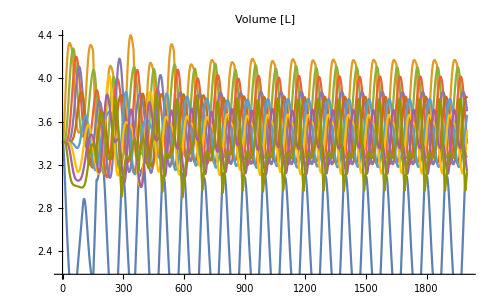

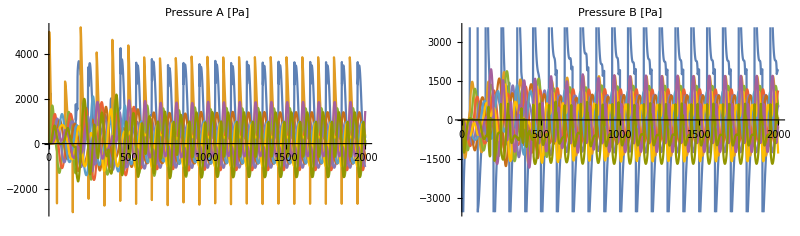

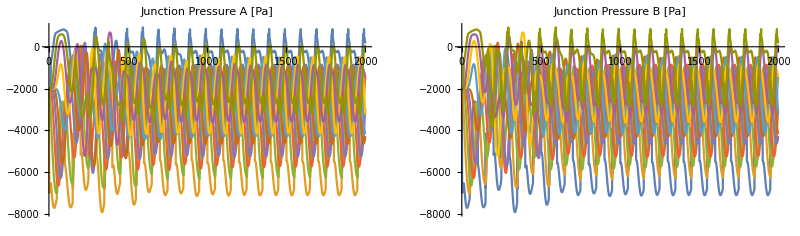

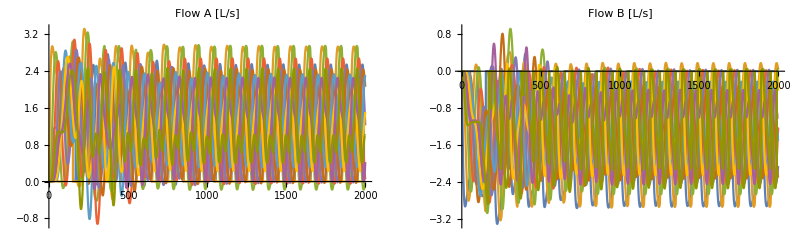

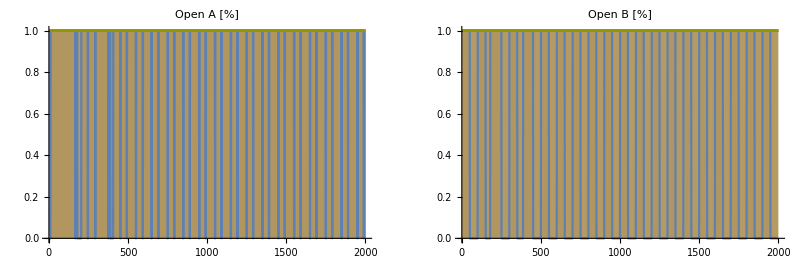

```mathematica
ListPlot[Transpose[state[[All,All,3]]]1000,Joined->True,PlotLabel->"Volume [L]"]
GraphicsRow[{ListPlot[Transpose[state[[All,All,4]]],Joined->True,PlotLabel->"Pressure A [Pa]"],
ListPlot[Transpose[state[[All,All,5]]],Joined->True,PlotLabel->"Pressure B [Pa]"]}]
GraphicsRow[{ListPlot[Transpose[state[[All,All,6]]],Joined->True,PlotLabel->"Junction Pressure A [Pa]"],
ListPlot[Transpose[state[[All,All,7]]],Joined->True,PlotLabel->"Junction Pressure B [Pa]"]}]
GraphicsRow[{ListPlot[Transpose[state[[All,All,8]]]1000,Joined->True,PlotLabel->"Flow A [L/s]"],
ListPlot[Transpose[state[[All,All,9]]]1000,Joined->True,PlotLabel->"Flow B [L/s]"]}]
GraphicsRow[{ListPlot[Transpose[state[[All,All,10]]],Joined->True,PlotLabel->"Open A [%]",Filling->Axis],
ListPlot[Transpose[state[[All,All,11]]],Joined->True,PlotLabel->"Open B [%]",Filling->Axis]}]
```

```mathematica
frame=10;
uVol=state[[frame,All,3]]
uFlowA=state[[frame,All,8]]
uFlowB=state[[frame,All,9]]
uOpenA=state[[frame,All,10]]
uOpenB=state[[frame,All,11]]
```

{0.00315656,0.00365079,0.003419,0.00340903,0.00340885,0.00340885,0.00340885,0.00340885,0.00340885,0.00340885}

{0,0.00229448,0.000176211,4.27086×10^-6,5.29574×10^-8,4.0193×10^-10,2.04869×10^-12,-2.60677×10^-14,-3.0126×10^-12,-1.42259×10^-10}

{-0.00229448,-0.000176211,-4.27086×10^-6,-5.29574×10^-8,-4.0193×10^-10,-2.04869×10^-12,2.60677×10^-14,3.0126×10^-12,1.42259×10^-10,0}

{0,1,1,1,1,1,1,1,1,1}

{1,1,1,1,1,1,1,1,1,1}

```mathematica
Clear[plotPipeRing,plotValveRing]
plotPipeRing[radii_List,r0_List]:=Table[
With[{r=1+2(radii[[i]]/r0[[i]]-1),θ=i/(Length@radii)2π,dθ=(2π)/(Length@radii)},
{
If[i==1,Darker@Blue,Black],
Annulus[{0,0},{10-r,10+r},{θ,θ+dθ}]
}
],
{i,Length@radii}]
plotValveRing[openA_,openB_]:=Table[
With[{r=10,θ=i/(Length@openA)2π,dθ=(2π)/(Length@openA)},
{
If[openA[[i]]>0.5,Green,Red],
Annulus[{0,0},{10-.25,10+.25},{θ+0.1dθ,θ+0.2dθ}],
If[openB[[i]]>0.5,Green,Red],
Annulus[{0,0},{10-.25,10+.25},{θ+0.8dθ,θ+0.9dθ}]
}
],
{i,Length@openA}]
With[{
vol=state[[All,All,3]],
openA=state[[All,All,10]],
openB=state[[All,All,11]]
},
Manipulate[Graphics[{
plotPipeRing[vol[[i]],Table[0.0031,{i,Length@vol}]],
plotValveRing[openA[[i]],openB[[i]]]
},
PlotRange->{{-15,15},{-15,15}}
],{i,1,Length@vol,1}
]]
```